```mathematica
(*measCond = 1.40*^-9; PREVIOUSLY*)
```

```mathematica
measCond = 1.399*^-9;
preFactor = 2.680594*^-08;
```

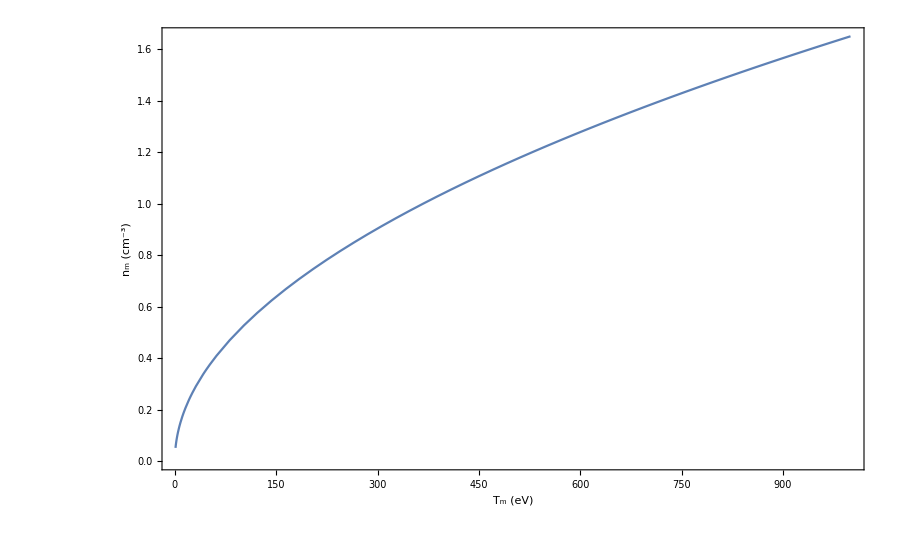

```mathematica
Plot[measCond/preFactor*√T,{T,1,1000},Frame->True,FrameLabel->{"T_m (eV)","n_m (cm^-3)"},ImageSize->900]
```

```mathematica
qMaxF[Ep_,Tm_]:=1+2(√(Ep/Tm))/Erfc[-√(Ep/Tm)] NIntegrate[Erfc[x],{x,-√(Ep/Tm),∞}]
```

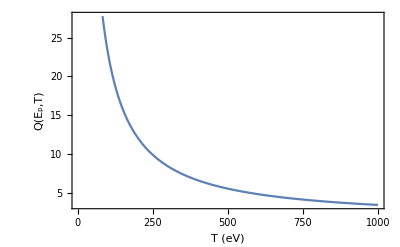

```mathematica
Plot[qMaxF[1108,T],{T,1,1000},Frame->True,FrameLabel->{"T (eV)","Q(E_p,T)"}]
```